```mathematica
fD1 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D1_v1.csv"];
fD2 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D2_v1.csv"];
fD1 = Flatten@fD1;
fD2 = Flatten@fD2;
```

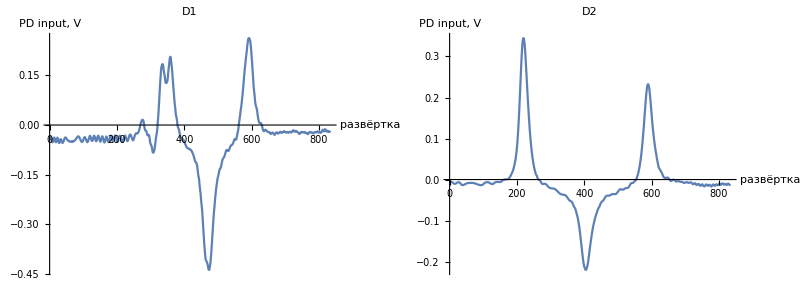

```mathematica
scale = 240;
image = Multicolumn[{
ListPlot[fD1, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D1", AxesLabel->{"развёртка", "PD input, V"}],
ListPlot[fD2, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D2", AxesLabel->{"развёртка", "PD input, V"}]
}]
```

```mathematica
(* отнормируем *)
αx = 10. /Length@fD2
xs =αx Range[Length@fD2] ;
data = Transpose[{xs, Flatten@fD2}];
```

0.0119904

```mathematica
color1 = RGBColor[0.27,0.25,1.]
```

RGBColor[0.27, 0.25, 1.]

## Подготовка

```mathematica
d1 = 140;
d2 = 300;
d3 = 500;
d4 = 700;
```

{a→0.3823,x0→2.64064,σ→-0.163466,c→-0.0283009}

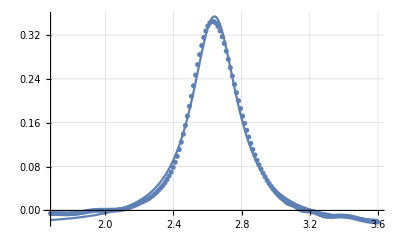

```mathematica
si = d1;
ei = d2;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c}, {a, {x0, αx/2(si + ei)}, σ, c}, x]
{aV1, x0V1, σV1, cV1} = {a, x0, σ, c}/.fit;
f1[x_] := aV1 σV1^2/((x-x0V1)^2+σV1^2) + cV1;
Show[{
Plot[f1[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All, GridLines->Automatic],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

{a→-0.200161,x0→4.85832,σ→0.237451,c→-0.0209153}

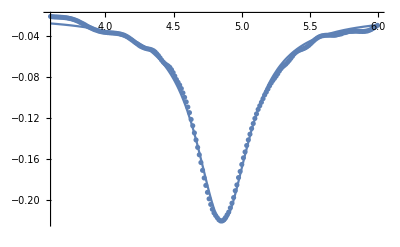

```mathematica
si = d2;
ei = d3;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c}, {a, {x0, αx/2(si + ei)}, σ, c}, x]
{aV2, x0V2, σV2, c2V2} = {a, x0, σ, c}/.fit;
f2[x_] := aV2 σV2^2/((x-x0V2)^2+σV2^2) + c2V2;
Show[{
Plot[f2[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

{a→0.25956,x0→7.07919,σ→0.180715,c2→-0.0223874}

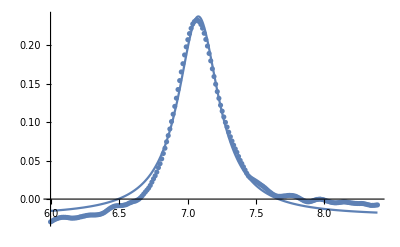

```mathematica
si = d3;
ei = d4;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c2}, {{a, 0.37}, {x0, 7}, {σ, 0.135}, c2}, x]
{aV3, x0V3, σV3, c2V3} = {a, x0, σ, c2}/.fit;
f3[x_] := aV3 σV3^2/((x-x0V3)^2+σV3^2) + c2V3;
Show[{
Plot[f3[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

## Фит

{a1→0.379467,x01→2.64094,σ1→-0.159037,a2→-0.199551,x02→4.85887,σ2→0.255615,a3→0.260075,x03→7.07848,σ3→0.183082,c→-0.0214244}

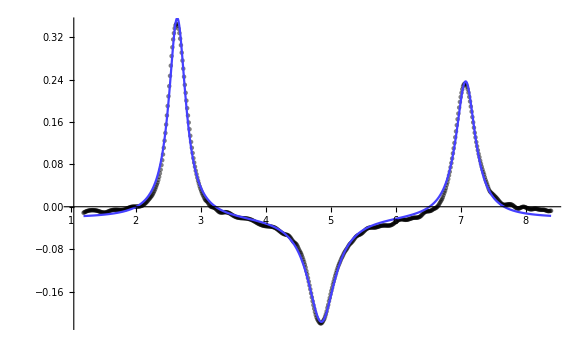

```mathematica
si = 100;
ei = 700;
nlm = NonlinearModelFit[data⟦si;;ei⟧, 
a1 σ1^2/((x-x01)^2+σ1^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2)+ c, 
{{a1, aV1}, {x01, x0V1}, {σ1, σV1},
{a2, aV2}, {x02, x0V2}, {σ2,σV2},
{a3, aV3}, {x03, x0V3}, {σ3, σV3}, c},x];
fit0 = nlm["BestFitParameters"]
f0[x_] :=a1 σ1^2/((x-x01)^2+σ1^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2)+ c /. fit0;
im1 = Show[{
ListPlot[data⟦si;;ei⟧, PlotRange->All, Joined->False, PlotStyle->{Black, Opacity[0.5]}],
Plot[f0[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All, PlotStyle->color1]
}]
```

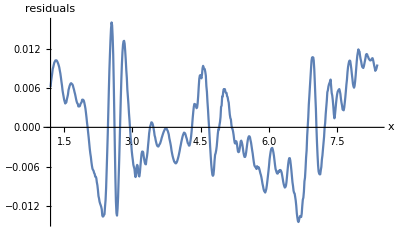

```mathematica
im2 = ListPlot[Transpose[{xs⟦si;;ei⟧,nlm["FitResiduals"]}], Joined->True, AxesLabel->{"x", "residuals"}, PlotRange->{{si αx, ei αx}, Automatic}]
```

```mathematica
nlm["ParameterTable"]
```

General::munfl: Exp[-1185.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2842.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-919.169] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 0.379467 | 0.00213199 | 177.987 | 0.
x01 | 2.64094 | 0.000891308 | 2962.99 | 0.
σ1 | -0.159037 | 0.00142158 | -111.874 | 0.
a2 | -0.199551 | 0.00169018 | -118.065 | 0.
x02 | 4.85887 | 0.00214946 | 2260.51 | 0.
σ2 | 0.255615 | 0.00357145 | 71.5719 | 2.38932×10^-293
a3 | 0.260075 | 0.00199034 | 130.669 | 0.
x03 | 7.07848 | 0.00139547 | 5072.48 | 0.
σ3 | 0.183082 | 0.00224095 | 81.6987 | 0.
c | -0.0214244 | 0.000532482 | -40.2351 | 2.12564×10^-171

## Обработка

```mathematica
Print["Отклонение CR: ", ((x03 + x01)/2 - x02)/x02 * 100 /. fit0, "%"]
```

Отклонение CR: 0.0171207%

```mathematica
dots2freq = 803.5 / (x03 - x01) /. fit0
```

181.069

```mathematica
σerrs = nlm["ParameterErrors"]⟦{3, 6, 9}⟧ 
Print["FWHM I:   ", 2Abs[σ1] dots2freq /. fit0,"±",  dots2freq σerrs⟦1⟧, " МГц"]
Print["FWHM II:  ", 2Abs[σ2] dots2freq /. fit0,"±",  dots2freq σerrs⟦2⟧, " МГц"]
Print["FWHM III: ",2 Abs[σ3] dots2freq /. fit0,"±",  dots2freq σerrs⟦3⟧, " МГц"]
```

{0.00142158,0.00357145,0.00224095}

FWHM I:   57.5934±0.257403 МГц

FWHM II:  92.568±0.646678 МГц

FWHM III: 66.301±0.405765 МГц

```mathematica
(* ±% от scale err *)
(Plus@@nlm["ParameterErrors"]⟦{2,8}⟧/ (x03 - x01) /. fit0)100
```

0.0515325

```mathematica
nlm["BestFitParameters"]
```

{a1→0.379467,x01→2.64094,σ1→-0.159037,a2→-0.199551,x02→4.85887,σ2→0.255615,a3→0.260075,x03→7.07848,σ3→0.183082,c→-0.0214244}